```mathematica
Quit[]
```

# Muon Production in SM - γ-> μ^- μ^+

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Remove[q1]
Remove[q2]
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[1]} -> {F[2,{2}], -F[2,{2}]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/kinematics.m already exist. It will NOT be overwritten.

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing,NoLightFHCoupling}, ExcludeParticles-> {}];
```

```mathematica
process={V[1]} -> {F[2,{2}], -F[2,{2}]};
```

```mathematica
topologiesBorn=CreateTopologies[0,1-> 2];
```

```mathematica
topologies1L=CreateTopologies[1,1-> 2,ExcludeTopologies->Reducible];
```

```mathematica
fieldsBorn=InsertFields[topologiesBorn, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

Excluding 48 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

Restoring 48 field point(s)

in total: 1 Particles insertion

```mathematica
fields1L=InsertFields[topologies1L, process];
```

Excluding 48 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 3 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 48 field point(s)

in total: 3 Particles insertions

```mathematica
ampBorn=CreateFeynAmp[fieldsBorn];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

in total: 3 Particles amplitudes

> Top. 1 ad/bdcd/0.m, 0 diagrams

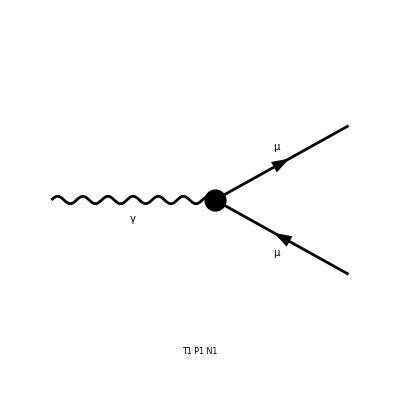

```mathematica
Paint[fieldsBorn];
```

> Top. 1 ad/becf/dedfef.m, 0 diagrams

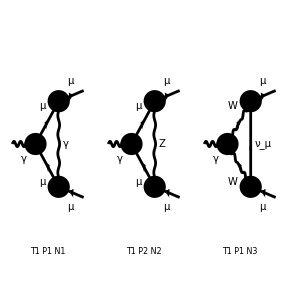

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L];
myAmpBorn=ExtractAmplitude[ampBorn];
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
SaveAmplitudes[myAmpBorn,"BornAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/feynArts_amplitudes/OneLoopAmplitudes.m

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/feynArts_amplitudes/BornAmplitudes.m

## Polarization Sums

```mathematica
sumEP={PolarizationVector[V[k_],p_,{mu_}]*PolarizationVector[V[k_],p_,{nu_}]->-SP[{mu},{nu}]}
```

{ep[V[k_],p_,{mu_}] ep[V[k_],p_,{nu_}]→-SP[{mu},{nu}]}

```mathematica
smPolarized=Map[AmpSquare[#,myAmpBorn][[1]]&,myAmp1L];
```

```mathematica
smUnPolarized=smPolarized/.sumEP//Expand//Simplify
```

{1/(8 π^4)ⅈ EL^4 gAl^4 KiraPropagator[q1,MM] KiraPropagator[-p1+q1,MM] KiraPropagator[-p2+q1,0] (-4 d MM^4+2 d^2 MM^4+4 d MM^2 mmsq-2 d^2 MM^2 mmsq+6 d MM^2 psq-d^2 MM^2 psq+8 MM^2 SP[p1,q1]-4 d MM^2 SP[p1,q1]+2 d^2 MM^2 SP[p1,q1]-8 mmsq SP[p1,q1]+8 d mmsq SP[p1,q1]-2 d^2 mmsq SP[p1,q1]-4 psq SP[p1,q1]+4 d psq SP[p1,q1]-8 MM^2 SP[p2,p2]+4 d MM^2 SP[p2,p2]-8 SP[p1,q1] SP[p2,p2]+4 d SP[p1,q1] SP[p2,p2]-8 SP[p1,p1] (MM^2-SP[p2,q1])-8 d MM^2 SP[p2,q1]+12 psq SP[p2,q1]-14 d psq SP[p2,q1]+2 d^2 psq SP[p2,q1]+16 SP[p1,q1] SP[p2,q1]-8 d SP[p1,q1] SP[p2,q1]-16 SP[p2,q1]^2+8 d SP[p2,q1]^2-8 MM^2 SP[q1,q1]+8 d MM^2 SP[q1,q1]-2 d^2 MM^2 SP[q1,q1]+8 mmsq SP[q1,q1]-8 d mmsq SP[q1,q1]+2 d^2 mmsq SP[q1,q1]-4 psq SP[q1,q1]+4 d psq SP[q1,q1]-d^2 psq SP[q1,q1]+8 SP[p2,p2] SP[q1,q1]-4 d SP[p2,p2] SP[q1,q1]+4 SP[p1,p2] (2 MM^2-2 SP[p1,q1]-(-2+d) SP[p2,q1]-2 SP[q1,q1]+d SP[q1,q1])),1/(16 π^4)ⅈ EL^4 gAl^2 KiraPropagator[q1,MM] KiraPropagator[-p1+q1,MM] KiraPropagator[-p2+q1,MZ] (-4 d gZlL^2 MM^4+2 d^2 gZlL^2 MM^4-4 d gZlR^2 MM^4+2 d^2 gZlR^2 MM^4+4 d gZlL^2 MM^2 mmsq-2 d^2 gZlL^2 MM^2 mmsq+4 d gZlR^2 MM^2 mmsq-2 d^2 gZlR^2 MM^2 mmsq-2 d gZlL^2 MM^2 psq+d^2 gZlL^2 MM^2 psq+16 d gZlL gZlR MM^2 psq-4 d^2 gZlL gZlR MM^2 psq-2 d gZlR^2 MM^2 psq+d^2 gZlR^2 MM^2 psq+8 gZlL^2 MM^2 SP[p1,q1]-8 d gZlL^2 MM^2 SP[p1,q1]+2 d^2 gZlL^2 MM^2 SP[p1,q1]+8 d gZlL gZlR MM^2 SP[p1,q1]+8 gZlR^2 MM^2 SP[p1,q1]-8 d gZlR^2 MM^2 SP[p1,q1]+2 d^2 gZlR^2 MM^2 SP[p1,q1]-8 gZlL^2 mmsq SP[p1,q1]+8 d gZlL^2 mmsq SP[p1,q1]-2 d^2 gZlL^2 mmsq SP[p1,q1]-8 gZlR^2 mmsq SP[p1,q1]+8 d gZlR^2 mmsq SP[p1,q1]-2 d^2 gZlR^2 mmsq SP[p1,q1]-4 gZlL^2 psq SP[p1,q1]+4 d gZlL^2 psq SP[p1,q1]-4 gZlR^2 psq SP[p1,q1]+4 d gZlR^2 psq SP[p1,q1]-8 gZlL^2 MM^2 SP[p2,p2]+4 d gZlL^2 MM^2 SP[p2,p2]-8 gZlR^2 MM^2 SP[p2,p2]+4 d gZlR^2 MM^2 SP[p2,p2]-8 gZlL^2 SP[p1,q1] SP[p2,p2]+4 d gZlL^2 SP[p1,q1] SP[p2,p2]-8 gZlR^2 SP[p1,q1] SP[p2,p2]+4 d gZlR^2 SP[p1,q1] SP[p2,p2]-16 d gZlL gZlR MM^2 SP[p2,q1]+12 gZlL^2 psq SP[p2,q1]-14 d gZlL^2 psq SP[p2,q1]+2 d^2 gZlL^2 psq SP[p2,q1]+12 gZlR^2 psq SP[p2,q1]-14 d gZlR^2 psq SP[p2,q1]+2 d^2 gZlR^2 psq SP[p2,q1]+16 gZlL^2 SP[p1,q1] SP[p2,q1]-8 d gZlL^2 SP[p1,q1] SP[p2,q1]+16 gZlR^2 SP[p1,q1] SP[p2,q1]-8 d gZlR^2 SP[p1,q1] SP[p2,q1]-16 gZlL^2 SP[p2,q1]^2+8 d gZlL^2 SP[p2,q1]^2-16 gZlR^2 SP[p2,q1]^2+8 d gZlR^2 SP[p2,q1]^2+8 SP[p1,p1] (-2 gZlL gZlR MM^2+(gZlL^2+gZlR^2) SP[p2,q1])-8 gZlL^2 MM^2 SP[q1,q1]+8 d gZlL^2 MM^2 SP[q1,q1]-2 d^2 gZlL^2 MM^2 SP[q1,q1]-8 gZlR^2 MM^2 SP[q1,q1]+8 d gZlR^2 MM^2 SP[q1,q1]-2 d^2 gZlR^2 MM^2 SP[q1,q1]+8 gZlL^2 mmsq SP[q1,q1]-8 d gZlL^2 mmsq SP[q1,q1]+2 d^2 gZlL^2 mmsq SP[q1,q1]+8 gZlR^2 mmsq SP[q1,q1]-8 d gZlR^2 mmsq SP[q1,q1]+2 d^2 gZlR^2 mmsq SP[q1,q1]-4 gZlL^2 psq SP[q1,q1]+4 d gZlL^2 psq SP[q1,q1]-d^2 gZlL^2 psq SP[q1,q1]-4 gZlR^2 psq SP[q1,q1]+4 d gZlR^2 psq SP[q1,q1]-d^2 gZlR^2 psq SP[q1,q1]+8 gZlL^2 SP[p2,p2] SP[q1,q1]-4 d gZlL^2 SP[p2,p2] SP[q1,q1]+8 gZlR^2 SP[p2,p2] SP[q1,q1]-4 d gZlR^2 SP[p2,p2] SP[q1,q1]-4 SP[p1,p2] (-2 gZlL^2 MM^2+d gZlL^2 MM^2-2 d gZlL gZlR MM^2-2 gZlR^2 MM^2+d gZlR^2 MM^2+2 (gZlL^2+gZlR^2) SP[p1,q1]+(-2+d) (gZlL^2+gZlR^2) SP[p2,q1]+2 gZlL^2 SP[q1,q1]-d gZlL^2 SP[q1,q1]+2 gZlR^2 SP[q1,q1]-d gZlR^2 SP[q1,q1])),-1/(16 π^4)ⅈ EL^4 gAl gWlN gWNl gWWA KiraPropagator[q1,MW] KiraPropagator[-p1+q1,MW] KiraPropagator[-p2+q1,0] (d MM^2 psq-7 d mmsq psq+2 d psq^2+4 MM^2 SP[p1,q1]-4 d MM^2 SP[p1,q1]-16 mmsq SP[p1,q1]+8 d mmsq SP[p1,q1]+6 psq SP[p1,q1]-5 d psq SP[p1,q1]+8 psq SP[p2,p2]-2 (-6+d) SP[p1,p1] (mmsq-SP[p2,q1])+8 MM^2 SP[p2,q1]-8 d MM^2 SP[p2,q1]+16 mmsq SP[p2,q1]-8 psq SP[p2,q1]+4 d psq SP[p2,q1]+16 SP[p1,q1] SP[p2,q1]-8 d SP[p1,q1] SP[p2,q1]-16 SP[p2,p2] SP[p2,q1]-16 SP[p2,q1]^2+8 d SP[p2,q1]^2+2 SP[p1,p2] (-2 MM^2+d MM^2-4 mmsq+d mmsq-4 psq+(2+d) SP[p1,q1]-2 (-6+d) SP[p2,q1]-4 SP[q1,q1])-8 MM^2 SP[q1,q1]+8 d MM^2 SP[q1,q1]+8 mmsq SP[q1,q1]-8 d mmsq SP[q1,q1]-4 psq SP[q1,q1]+4 d psq SP[q1,q1]+8 SP[p2,p2] SP[q1,q1])}

## Interference

```mathematica
test=AmpSquare[myAmp1L[[3]],myAmpBorn[[1]]]//Simplify
```

-1/(16 π^4)ⅈ EL^4 gAl gWlN gWNl gWWA KiraPropagator[q1,MW] KiraPropagator[-p1+q1,MW] KiraPropagator[-p2+q1,0] ep[V[1],p1,{Lor1}] ep[V[1],p1,{newLor1}] (-8 psq SP[p2,{Lor1}] SP[p2,{newLor1}]+16 SP[p2,q1] SP[p2,{Lor1}] SP[p2,{newLor1}]-8 SP[p2,{Lor1}] SP[p2,{newLor1}] SP[q1,q1]-12 MM^2 SP[p2,{newLor1}] SP[q1,{Lor1}]+4 d MM^2 SP[p2,{newLor1}] SP[q1,{Lor1}]-12 mmsq SP[p2,{newLor1}] SP[q1,{Lor1}]+4 d mmsq SP[p2,{newLor1}] SP[q1,{Lor1}]-8 SP[p1,q1] SP[p2,{newLor1}] SP[q1,{Lor1}]+4 d SP[p1,q1] SP[p2,{newLor1}] SP[q1,{Lor1}]+16 SP[p2,q1] SP[p2,{newLor1}] SP[q1,{Lor1}]-8 d SP[p2,q1] SP[p2,{newLor1}] SP[q1,{Lor1}]+2 SP[p1,{newLor1}] (SP[p2,{Lor1}] (-MM^2+mmsq+2 psq-4 SP[p1,q1]-4 SP[p2,q1]+2 SP[q1,q1])+(MM^2+5 mmsq-2 d mmsq+2 (-2+d) SP[p2,q1]) SP[q1,{Lor1}])+4 MM^2 SP[p2,{Lor1}] SP[q1,{newLor1}]-4 mmsq SP[p2,{Lor1}] SP[q1,{newLor1}]+8 psq SP[p2,{Lor1}] SP[q1,{newLor1}]+8 MM^2 SP[q1,{Lor1}] SP[q1,{newLor1}]-4 d MM^2 SP[q1,{Lor1}] SP[q1,{newLor1}]-8 mmsq SP[q1,{Lor1}] SP[q1,{newLor1}]+4 d mmsq SP[q1,{Lor1}] SP[q1,{newLor1}]+4 psq SP[q1,{Lor1}] SP[q1,{newLor1}]-2 d psq SP[q1,{Lor1}] SP[q1,{newLor1}]+SP[p1,{Lor1}] (2 (-6+d) SP[p1,{newLor1}] (mmsq-SP[p2,q1])-2 SP[p2,{newLor1}] (-3 MM^2+d MM^2-3 mmsq+d mmsq-2 psq+(-2+d) SP[p1,q1]-2 (-4+d) SP[p2,q1]-2 SP[q1,q1])+(2 (-3+d) MM^2-2 (-3+d) mmsq+(-6+d) psq) SP[q1,{newLor1}])-MM^2 psq SP[{Lor1},{newLor1}]+7 mmsq psq SP[{Lor1},{newLor1}]-2 psq^2 SP[{Lor1},{newLor1}]+2 MM^2 SP[p1,q1] SP[{Lor1},{newLor1}]-2 mmsq SP[p1,q1] SP[{Lor1},{newLor1}]+4 psq SP[p1,q1] SP[{Lor1},{newLor1}]+4 MM^2 SP[p2,q1] SP[{Lor1},{newLor1}]-4 mmsq SP[p2,q1] SP[{Lor1},{newLor1}]-4 psq SP[p2,q1] SP[{Lor1},{newLor1}]-4 MM^2 SP[q1,q1] SP[{Lor1},{newLor1}]+4 mmsq SP[q1,q1] SP[{Lor1},{newLor1}]-2 psq SP[q1,q1] SP[{Lor1},{newLor1}])

```mathematica
SquareSimplifyAndSave[smUnPolarized,{1}]
```

Computed contribution 1-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm//interferences/Contribution_1_1.m.

Computed contribution 2-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm//interferences/Contribution_2_1.m.

Computed contribution 3-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm//interferences/Contribution_3_1.m.

## Shift

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/input/kinematics.m.

```mathematica
ExtractFamily[test]
```

{{gamma,{MW}}}

```mathematica
ShiftToIntegralFamily[test]
```

{{q1→q1}}

```mathematica
Do[
ShiftAndSave[i,j,False],
{i,3},{j,1}]
```

Integral family {{gamma, {MM}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/interferences/Contribution_1_1.m.

Integral family {{zeta, {MM, MZ}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/interferences/Contribution_2_1.m.

Integral family {{gamma, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/interferences/Contribution_3_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,3},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/A-mm/kira_input/Contribution_3_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[gamma,{MM},1,1,1],userIntegral[gamma,{MM},0,1,1],userIntegral[gamma,{MM},1,0,1],userIntegral[gamma,{MM},1,1,0],userIntegral[gamma,{MM},-1,1,1],userIntegral[gamma,{MM},0,0,1],userIntegral[gamma,{MM},0,1,0],userIntegral[gamma,{MM},1,0,0],userIntegral[gamma,{MM},1,1,-1],userIntegral[zeta,{MM,MZ},1,1,1],userIntegral[zeta,{MM,MZ},0,1,1],userIntegral[zeta,{MM,MZ},1,0,1],userIntegral[zeta,{MM,MZ},1,1,0],userIntegral[zeta,{MM,MZ},-1,1,1],userIntegral[zeta,{MM,MZ},0,0,1],userIntegral[zeta,{MM,MZ},0,1,0],userIntegral[zeta,{MM,MZ},1,0,0],userIntegral[zeta,{MM,MZ},1,1,-1],userIntegral[gamma,{MW},1,1,1],userIntegral[gamma,{MW},0,1,1],userIntegral[gamma,{MW},1,0,1],userIntegral[gamma,{MW},1,1,0],userIntegral[gamma,{MW},-1,1,1],userIntegral[gamma,{MW},0,0,1],userIntegral[gamma,{MW},0,1,0],userIntegral[gamma,{MW},1,0,0],userIntegral[gamma,{MW},1,1,-1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[gamma,{m1},0,0,1]→0,userIntegral[gamma,{m1},0,1,1]→userIntegral[gamma,{m1},1,0,1],userIntegral[gamma,{m1},-1,1,1]→(psq userIntegral[gamma,{m1},1,0,0])/(2 mmsq)+((-m1^2 psq+mmsq psq) userIntegral[gamma,{m1},1,0,1])/(2 mmsq),userIntegral[gamma,{m1},0,1,0]→userIntegral[gamma,{m1},1,0,0],userIntegral[gamma,{m1},1,1,-1]→userIntegral[gamma,{m1},1,0,0]+1/2 (2 m1^2+2 mmsq-psq) userIntegral[gamma,{m1},1,1,0],userIntegral[zeta,{m1,m2},0,1,1]→userIntegral[zeta,{m1,m2},1,0,1],userIntegral[zeta,{m1,m2},1,1,0]→userIntegral[gamma,{m1},1,1,0],userIntegral[zeta,{m1,m2},-1,1,1]→(psq userIntegral[gamma,{m1},1,0,0])/(2 mmsq)+((2 mmsq-psq) userIntegral[zeta,{m1,m2},0,0,1])/(2 mmsq)+((-m1^2 psq+m2^2 psq+mmsq psq) userIntegral[zeta,{m1,m2},1,0,1])/(2 mmsq),userIntegral[zeta,{m1,m2},0,1,0]→userIntegral[gamma,{m1},1,0,0],userIntegral[zeta,{m1,m2},1,0,0]→userIntegral[gamma,{m1},1,0,0],userIntegral[zeta,{m1,m2},1,1,-1]→userIntegral[gamma,{m1},1,0,0]+1/2 (2 m1^2-2 m2^2+2 mmsq-psq) userIntegral[gamma,{m1},1,1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[gamma,{MM},1,1,1],userIntegral[gamma,{MM},0,1,1],userIntegral[gamma,{MM},1,0,1],userIntegral[gamma,{MM},1,1,0],userIntegral[gamma,{MM},-1,1,1],userIntegral[gamma,{MM},0,0,1],userIntegral[gamma,{MM},0,1,0],userIntegral[gamma,{MM},1,0,0],userIntegral[gamma,{MM},1,1,-1],userIntegral[zeta,{MM,MZ},1,1,1],userIntegral[zeta,{MM,MZ},0,1,1],userIntegral[zeta,{MM,MZ},1,0,1],userIntegral[zeta,{MM,MZ},1,1,0],userIntegral[zeta,{MM,MZ},-1,1,1],userIntegral[zeta,{MM,MZ},0,0,1],userIntegral[zeta,{MM,MZ},0,1,0],userIntegral[zeta,{MM,MZ},1,0,0],userIntegral[zeta,{MM,MZ},1,1,-1],userIntegral[gamma,{MW},1,1,1],userIntegral[gamma,{MW},0,1,1],userIntegral[gamma,{MW},1,0,1],userIntegral[gamma,{MW},1,1,0],userIntegral[gamma,{MW},-1,1,1],userIntegral[gamma,{MW},0,0,1],userIntegral[gamma,{MW},0,1,0],userIntegral[gamma,{MW},1,0,0],userIntegral[gamma,{MW},1,1,-1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[gamma,{MM},1,1,1],userIntegral[gamma,{MM},1,0,1],userIntegral[gamma,{MM},1,1,0],userIntegral[gamma,{MM},1,0,0],userIntegral[zeta,{MM,MZ},1,1,1],userIntegral[zeta,{MM,MZ},1,0,1],userIntegral[zeta,{MM,MZ},0,0,1],userIntegral[gamma,{MW},1,1,1],userIntegral[gamma,{MW},1,0,1],userIntegral[gamma,{MW},1,1,0],userIntegral[gamma,{MW},1,0,0]}

```mathematica
Do[
SaveResult[i,j];
,{i,3},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,3}]
```

```mathematica
diagramCoefficients;//Simplify
```

```mathematica
coefficients=Plus@@diagramCoefficients//Simplify
```

{(ⅈ EL^4 gAl^4 ((-6+d) MM^4+(-2+d) (mmsq-psq)^2+MM^2 (-2 d mmsq+4 psq)))/(4 π^4),-(ⅈ EL^4 gAl^4 ((8-4 d+d^2) MM^2-(-2+d) ((-2+d) mmsq-2 psq)))/(4 π^4),-1/(16 π^4)ⅈ EL^4 gAl^2 (-4 (2+d) gAl^2 MM^2-8 d gZlL gZlR MM^2+2 (-2+d) gAl^2 (2 mmsq+(-7+d) psq)+(-2+d) gZlL^2 (2 MM^2+2 mmsq-2 MZ^2-7 psq+d psq)+(-2+d) gZlR^2 (2 MM^2+2 mmsq-2 MZ^2-7 psq+d psq)),-(ⅈ (-2+d) EL^4 gAl^2 (2 gAl^2+gZlL^2+gZlR^2))/(8 π^4),1/(16 π^4)ⅈ EL^4 gAl^2 (-4 gZlL gZlR MM^2 (2 d (MM^2+mmsq-MZ^2-3 psq)+4 psq+d^2 psq)+(-2+d) gZlL^2 (6 MM^4+2 mmsq^2+2 MZ^4+8 MZ^2 psq-d MZ^2 psq+2 psq^2-4 mmsq (MZ^2+psq)+MM^2 (-4 MZ^2+2 (-4+d) psq))+(-2+d) gZlR^2 (6 MM^4+2 mmsq^2+2 MZ^4+8 MZ^2 psq-d MZ^2 psq+2 psq^2-4 mmsq (MZ^2+psq)+MM^2 (-4 MZ^2+2 (-4+d) psq))),-1/(8 π^4)ⅈ EL^4 gAl^2 (4 d gZlL gZlR MM^2+(-2+d) gZlL^2 ((-4+d) MM^2-(-2+d) mmsq+2 (MZ^2+psq))+(-2+d) gZlR^2 ((-4+d) MM^2-(-2+d) mmsq+2 (MZ^2+psq))),(ⅈ (-2+d) EL^4 gAl^2 (gZlL^2+gZlR^2))/(8 π^4),(ⅈ EL^4 gAl gWlN gWNl gWWA (mmsq-MW^2) (2 (-1+d) MM^2-(-2+d) (mmsq-MW^2-2 psq)))/(8 π^4),-(ⅈ EL^4 gAl gWlN gWNl gWWA ((-1+d) MM^2-(-2+d) (mmsq-MW^2-psq)))/(4 π^4),-(ⅈ EL^4 gAl gWlN gWNl gWWA (4 (-1+d) MM^2-(-2+d) (2 mmsq+2 MW^2+psq)))/(16 π^4),(ⅈ (-2+d) EL^4 gAl gWlN gWNl gWWA)/(8 π^4)}

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
```

```mathematica
parameterReplace=smparameters;
```

```mathematica
coefficients/.parameterReplace/.{psq->0,mmsq->MM^2}//Simplify
```

{-(2 ⅈ EL^4 MM^4)/π^4,-(ⅈ EL^4 MM^2)/π^4,(ⅈ EL^4 ((-2+d) MZ^2 (1-4 SW^2+8 SW^4)-2 MM^2 (d-2 (1+(-4+8 CW^2) SW^2+8 SW^4))))/(32 CW^2 π^4 SW^2),-(ⅈ (-2+d) EL^4 (1+(-4+8 CW^2) SW^2+8 SW^4))/(32 CW^2 π^4 SW^2),(ⅈ EL^4 (2 MM^2-MZ^2) (2 MM^2 (-2+d+8 SW^2-16 SW^4)-(-2+d) MZ^2 (1-4 SW^2+8 SW^4)))/(32 CW^2 π^4 SW^2),(ⅈ EL^4 (MM^2 (-2+d+8 SW^2-16 SW^4)-(-2+d) MZ^2 (1-4 SW^2+8 SW^4)))/(16 CW^2 π^4 SW^2),(ⅈ (-2+d) EL^4 (1-4 SW^2+8 SW^4))/(32 CW^2 π^4 SW^2),(ⅈ EL^4 (MM^2-MW^2) (-2 MW^2+d (MM^2+MW^2)))/(16 π^4 SW^2),-(ⅈ EL^4 (MM^2+(-2+d) MW^2))/(8 π^4 SW^2),(ⅈ EL^4 (-2 MW^2+d (-MM^2+MW^2)))/(16 π^4 SW^2),(ⅈ (-2+d) EL^4)/(16 π^4 SW^2)}

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[gamma,{MM},1,1,1],userIntegral[gamma,{MM},1,0,1],userIntegral[gamma,{MM},1,1,0],userIntegral[gamma,{MM},1,0,0],userIntegral[zeta,{MM,MZ},1,1,1],userIntegral[zeta,{MM,MZ},1,0,1],userIntegral[zeta,{MM,MZ},0,0,1],userIntegral[gamma,{MW},1,1,1],userIntegral[gamma,{MW},1,0,1],userIntegral[gamma,{MW},1,1,0],userIntegral[gamma,{MW},1,0,0]}